```mathematica
(*Import packages*)
(*<< PVReduce`*)
(*Remove[PVReduce`Dot];*)
$LoadAddOns={"FeynArts"};
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<<TreeLevel`
```

```mathematica
(*Why is this?*)
$KeepLogDivergentScalelessIntegrals=True;
```

## Get Feynman diagrams

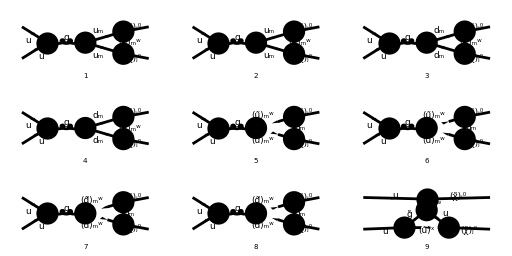

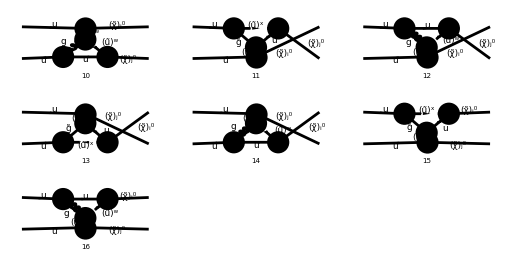

```mathematica
triDiagrams = InsertFields[CreateTopologies[1, 2->2,ExcludeTopologies->{Boxes,SelfEnergies,Tadpoles}], {F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling},ExcludeParticles->{V[1],V[2],V[3],F[11],F[12],S[1],S[2],S[3],S[4]}];
Paint[triDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

## Convert diagrams to amplitudes

```mathematica
(*Box-loop diagrams*)
Subscript[M, tri][0]=FCFAConvert[CreateFeynAmp[triDiagrams], IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,pj},LoopMomenta->{qloop},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν}]/.AmpSimplifyRules;
```

FCFAConvert::sumOverWarn: You are omitting SumOver objects that may represent a nontrivial summation. This may lead to a loss of overall factors multiplying some of your diagrams. Please make sure that this is really what you want.

```mathematica
(*Replacing couplings*)
Subscript[M, tri][1]=Simplify/@Subscript[M, tri][0]/.QSimplifyRules;
```

```mathematica
Subscript[M, tri][2]=TraceLoopAmp/@Subscript[M, tri][1];
```

```mathematica
Subscript[M, tri][3]=EvalPVLoopAmp/@SparseArray[Subscript[M, tri][2]]["NonzeroValues"];
CheckPVRemainder/@Subscript[M, tri][3]
```

{True,True,True,True,True,True,True,True}

```mathematica
Subscript[M, tri][4]=(SelectNotFree2[#1,{A0,B0,C0,D0}]&)/@Select[Subscript[M, tri][3],CheckPVRemainder]
```

## Compute interference with tree-level amplitudes

```mathematica
(Prefactor FullSimplify[SelectFree2[#1,DiracTrace]/Prefactor]&)/@Subscript[I, ttri][0]
```

ⅈ_ttri(0)

```mathematica
Subscript[I, stri][0]=FullSimplify/@(SelectFree2[#1,DiracTrace]&)/@SquareAmplitudes[Subscript[M, tri][4]/.{Index[Sfermion,5]->A,Index[Sfermion,6]->C},Subscript[M̄, s][0]]/.{SqrtEGl Conjugate[SqrtEGl]->1}/.SuperChargeRules
Subscript[I, ttri][0]=FullSimplify/@(SelectFree2[#1,DiracTrace]&)/@SquareAmplitudes[Subscript[M, tri][4]/.{Index[Sfermion,5]->A,Index[Sfermion,6]->C},Subscript[M̄, t][0]/.A->B]/.{SqrtEGl Conjugate[SqrtEGl]->1}/.SuperChargeRules
Subscript[I, utri][0]=FullSimplify/@(SelectFree2[#1,DiracTrace]&)/@SquareAmplitudes[Subscript[M, tri][4]/.{Index[Sfermion,5]->A,Index[Sfermion,6]->C},Subscript[M̄, u][0]/.A->B]/.{SqrtEGl Conjugate[SqrtEGl]->1}/.SuperChargeRules
```

{1/(4 π^2 (t-m_j^2) (t-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2)C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(m_j^2,0,m_((q̃)_C)^2) m_j (SqrtEGl Conjugate[(Z_s^L)] Conjugate[((Q̃)_(C,1))] C_iA^L (m_(g̃) SqrtEGl Conjugate[((Q̃)_(A,1))] C_jC^L-Conjugate[SqrtEGl] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] m_j) (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j (Conjugate[SqrtEGl] Conjugate[(C_iA^R)] Conjugate[(Z_s^R)] Conjugate[((Q̃)_(C,2))] (SqrtEGl Conjugate[((Q̃)_(A,1))] C_jC^L m_j-m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))])+SqrtEGl Conjugate[((Q̃)_(C,1))] C_iA^L (m_(g̃) SqrtEGl Conjugate[((Q̃)_(A,1))] C_jC^L-Conjugate[SqrtEGl] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] m_j) Z_s^L)+Conjugate[SqrtEGl] Conjugate[(C_iA^R)] Conjugate[((Q̃)_(C,2))] (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))]-SqrtEGl Conjugate[((Q̃)_(A,1))] C_jC^L m_j) (2 m_i^2 (m_j^2+t)-t (-2 m_j^2+D s+2 t+4 u)) Z_s^R)+B_0(t,0,m_(g̃)^2) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iA^L C_jC^L m_j (Conjugate[(Z_s^L)] (2 m_i^2 (m_j^2+t)-t (-2 m_j^2+D s+2 t+4 u))-(D-2) s m_i m_j Z_s^L) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iA^R)] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R)+t (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_iA^L (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L)-Conjugate[(C_iA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R)))+C_0(0,t,m_j^2,m_((q̃)_C)^2,m_(g̃)^2,0) (-m_(g̃) Conjugate[(C_iA^R)] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R) (Conjugate[SqrtEGl])^2+SqrtEGl Conjugate[(Z_s^L)] Conjugate[((Q̃)_(C,1))] C_iA^L (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) (m_(g̃) SqrtEGl Conjugate[((Q̃)_(A,1))] C_jC^L m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t)+Conjugate[SqrtEGl] Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] (t m_((q̃)_C)^2-m_(g̃)^2 m_j^2))+(D-2) m_(g̃) s SqrtEGl^2 Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iA^L C_jC^L m_i m_j^2 (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) Z_s^L+(m_(g̃)^2 m_j^2-t m_((q̃)_C)^2) (Conjugate[(C_iA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R)-(D-2) s Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_iA^L m_i m_j Z_s^L))),(C_F δ_ab (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (t-m_j^2)-B_0(t,0,m_((q̃)_A)^2) (m_j^2+t)-2 C_0(0,t,m_j^2,0,0,m_((q̃)_A)^2) (t-m_j^2) (m_j^2-m_((q̃)_A)^2)) g_s^2 g_W^4 δ_ab (Q_A^(L L̄) (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L)-Conjugate[(Q_A^(R R̄))] ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_i^2+D s+2 t+4 u)-2 (m_i^2+t) m_j^2) Z_s^R)))/(8 π^2 (t-m_j^2) (t-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2),1/(4 π^2 (u-m_j^2) (u-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2)C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(m_j^2,0,m_((q̃)_C)^2) m_j (Conjugate[SqrtEGl] Conjugate[(C_iA^L)] ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl C_iA^R (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R) (Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)-m_(g̃) SqrtEGl C_jC^R (Q̃)_(A,2)) (Q̃)_(C,2))+B_0(u,0,m_(g̃)^2) (-Conjugate[SqrtEGl] Conjugate[(C_iA^L)] ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_i^2+D s+4 t+2 u)-2 (m_i^2+u) m_j^2) Z_s^L) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)-SqrtEGl u C_jC^R (Q̃)_(A,2)) (Q̃)_(C,1)-SqrtEGl C_iA^R (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R) (u Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-m_(g̃) SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,2))+C_0(u,m_j^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (-m_(g̃) C_iA^R C_jC^R m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u) (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iA^L)] Conjugate[(C_jC^L)] m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u) ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L) (Q̃)_(A,1) (Q̃)_(C,1)+(m_(g̃)^2 m_j^2-u m_((q̃)_C)^2) (Conjugate[(C_jC^L)] C_iA^R (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R) (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(C_iA^L)] C_jC^R ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L) (Q̃)_(A,2) (Q̃)_(C,1)))),-(C_F δ_ab (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (u-m_j^2)-B_0(u,0,m_((q̃)_A)^2) (m_j^2+u)-2 C_0(u,m_j^2,0,0,m_((q̃)_A)^2,0) (u-m_j^2) (m_j^2-m_((q̃)_A)^2)) g_s^2 g_W^4 δ_ab (Q_A^(R R̄) (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)-Conjugate[(Q_A^(L L̄))] ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_i^2+D s+4 t+2 u)-2 (m_i^2+u) m_j^2) Z_s^L)))/(8 π^2 (u-m_j^2) (u-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2),1/(4 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2)C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(u,0,m_(g̃)^2) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L C_jA^L m_i ((2 m_i^2 (m_j^2+u)-u (-2 m_j^2+D s+4 t+2 u)) Z_s^L-(D-2) s Conjugate[(Z_s^L)] m_i m_j) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)+u (Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_jA^L ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L)-Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)))+B_0(m_i^2,0,m_((q̃)_C)^2) m_i (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L C_jA^L ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L) SqrtEGl^2-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)+m_i (Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)-Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_jA^L ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L)))+C_0(0,u,m_i^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L C_jA^L m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L) SqrtEGl^2-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)+(m_(g̃)^2 m_i^2-u m_((q̃)_C)^2) (Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)-Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_jA^L ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u)) Z_s^L)))),-(C_F δ_ab (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (u-m_i^2)-B_0(u,0,m_((q̃)_A)^2) (m_i^2+u)-2 C_0(0,u,m_i^2,0,0,m_((q̃)_A)^2) (u-m_i^2) (m_i^2-m_((q̃)_A)^2)) g_s^2 g_W^4 δ_ab (Q_A^(R R̄) (Conjugate[(Z_s^R)] (u (-2 m_j^2+D s+4 t+2 u)-2 m_i^2 (m_j^2+u))+(D-2) s m_i m_j Z_s^R)-Conjugate[(Q_A^(L L̄))] ((D-2) s Conjugate[(Z_s^L)] m_i m_j+(u (-2 m_i^2+D s+4 t+2 u)-2 (m_i^2+u) m_j^2) Z_s^L)))/(8 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2),1/(4 π^2 (t-m_i^2) (t-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2)C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(m_i^2,0,m_((q̃)_C)^2) m_i (Conjugate[SqrtEGl] Conjugate[(C_jA^L)] (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1)-SqrtEGl C_iC^R m_i (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl C_jA^R ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R) (Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i (Q̃)_(A,1)-m_(g̃) SqrtEGl C_iC^R (Q̃)_(A,2)) (Q̃)_(C,2))+B_0(t,0,m_(g̃)^2) (Conjugate[SqrtEGl] Conjugate[(C_jA^L)] (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L) (SqrtEGl t C_iC^R (Q̃)_(A,2)-m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i (Q̃)_(A,1)) (Q̃)_(C,1)+SqrtEGl C_jA^R ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_i^2+D s+2 t+4 u)-2 (m_i^2+t) m_j^2) Z_s^R) (m_(g̃) SqrtEGl C_iC^R m_i (Q̃)_(A,2)-t Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1)) (Q̃)_(C,2))+C_0(t,m_i^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (-m_(g̃) C_iC^R C_jA^R m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] Conjugate[(C_jA^L)] m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L) (Q̃)_(A,1) (Q̃)_(C,1)+(m_(g̃)^2 m_i^2-t m_((q̃)_C)^2) (Conjugate[(C_iC^L)] C_jA^R ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t)) Z_s^R) (Q̃)_(A,1) (Q̃)_(C,2)-Conjugate[(C_jA^L)] C_iC^R (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L) (Q̃)_(A,2) (Q̃)_(C,1)))),(C_F δ_ab (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (t-m_i^2)-B_0(t,0,m_((q̃)_A)^2) (m_i^2+t)-2 C_0(t,m_i^2,0,0,m_((q̃)_A)^2,0) (t-m_i^2) (m_i^2-m_((q̃)_A)^2)) g_s^2 g_W^4 δ_ab (Q_A^(L L̄) (Conjugate[(Z_s^L)] (t (-2 m_j^2+D s+2 t+4 u)-2 m_i^2 (m_j^2+t))+(D-2) s m_i m_j Z_s^L)-Conjugate[(Q_A^(R R̄))] ((D-2) s Conjugate[(Z_s^R)] m_i m_j+(t (-2 m_i^2+D s+2 t+4 u)-2 (m_i^2+t) m_j^2) Z_s^R)))/(8 π^2 (t-m_i^2) (t-m_((q̃)_A)^2) ((p_i+p_j)^2-m_Z^2) (cos(θ_W))^2)}

{1/(2 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_i^2) (B_0(t,0,m_(g̃)^2) (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))+t (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))+B_0(m_j^2,0,m_((q̃)_C)^2) m_j (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))-m_j (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))+C_0(0,t,m_j^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))-(m_(g̃)^2 m_j^2-t m_((q̃)_C)^2) (Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (t-m_i^2) (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (t-m_j^2)-B_0(t,0,m_((q̃)_A)^2) (m_j^2+t)-2 C_0(0,t,m_j^2,0,0,m_((q̃)_A)^2) (t-m_j^2) (m_j^2-m_((q̃)_A)^2)) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))) g_s^2 g_W^4 δ_ab)/(4 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(2 π^2 (u-m_j^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(m_j^2,0,m_((q̃)_C)^2) m_j (Conjugate[SqrtEGl] (Conjugate[(Q_B^LR)] C_iA^R (t u-m_i^2 m_j^2)-s Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i m_j) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,1)-SqrtEGl (Conjugate[(C_iA^L)] (t u-m_i^2 m_j^2) Q_B^RL-s C_iA^R m_i m_j Q_B^(R R̄)) (Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)-m_(g̃) SqrtEGl C_jC^R (Q̃)_(A,2)) (Q̃)_(C,2))+B_0(u,0,m_(g̃)^2) (Conjugate[SqrtEGl] (Conjugate[(Q_B^LR)] C_iA^R (t u-m_i^2 m_j^2)-s Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i m_j) (SqrtEGl u C_jC^R (Q̃)_(A,2)-m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)) (Q̃)_(C,1)+SqrtEGl (Conjugate[(C_iA^L)] (t u-m_i^2 m_j^2) Q_B^RL-s C_iA^R m_i m_j Q_B^(R R̄)) (u Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-m_(g̃) SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,2))+C_0(u,m_j^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (m_(g̃) C_jC^R m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u) (Conjugate[(C_iA^L)] (t u-m_i^2 m_j^2) Q_B^RL-s C_iA^R m_i m_j Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^L)] m_j (Conjugate[(Q_B^LR)] C_iA^R (t u-m_i^2 m_j^2)-s Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i m_j) (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u) (Q̃)_(A,1) (Q̃)_(C,1)+(m_(g̃)^2 m_j^2-u m_((q̃)_C)^2) (C_jC^R (s Conjugate[(C_iA^L)] Conjugate[(Q_B^(L L̄))] m_i m_j+Conjugate[(Q_B^LR)] C_iA^R (m_i^2 m_j^2-t u)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_jC^L)] (Conjugate[(C_iA^L)] (m_i^2 m_j^2-t u) Q_B^RL+s C_iA^R m_i m_j Q_B^(R R̄)) (Q̃)_(A,1) (Q̃)_(C,2)))),(C_F δ_ab (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (u-m_j^2)-B_0(u,0,m_((q̃)_A)^2) (m_j^2+u)-2 C_0(u,m_j^2,0,0,m_((q̃)_A)^2,0) (u-m_j^2) (m_j^2-m_((q̃)_A)^2)) (Conjugate[(Q_B^LR)] (t u-m_i^2 m_j^2) Q_A^RL-Conjugate[(C_iA^L)] (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL)-s m_i m_j Q_A^(R R̄) Q_B^(R R̄)) g_s^2 g_W^4 δ_ab)/(4 π^2 (u-m_j^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(2 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (B_0(u,0,m_(g̃)^2) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L m_i (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (Conjugate[(Q_B^LR)] C_jA^L (m_i^2 m_j^2-t u)+s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄))+u (Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (t u-m_i^2 m_j^2)-Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL)-s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j Q_B^(R R̄)))+B_0(m_i^2,0,m_((q̃)_C)^2) m_i (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^LR)] C_jA^L (t u-m_i^2 m_j^2)-s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄))+m_i (Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (m_i^2 m_j^2-t u)+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL)+s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j Q_B^(R R̄)))+C_0(0,u,m_i^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (Conjugate[(C_jA^R)] (t u-m_i^2 m_j^2) Q_B^RL-s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (Conjugate[(Q_B^LR)] C_jA^L (t u-m_i^2 m_j^2)-s Conjugate[(C_jA^R)] m_i m_j Q_B^(R R̄))+(m_(g̃)^2 m_i^2-u m_((q̃)_C)^2) (Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L C_jA^L (m_i^2 m_j^2-t u)+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL)+s Conjugate[(C_jA^R)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L m_i m_j Q_B^(R R̄)))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (u-m_i^2)-B_0(u,0,m_((q̃)_A)^2) (m_i^2+u)-2 C_0(0,u,m_i^2,0,0,m_((q̃)_A)^2) (u-m_i^2) (m_i^2-m_((q̃)_A)^2)) (Conjugate[(Q_B^LR)] (t u-m_i^2 m_j^2) Q_A^RL-Conjugate[(C_iA^L)] (s Conjugate[(Q_B^(L L̄))] C_jA^L m_i m_j+Conjugate[(C_jA^R)] (m_i^2 m_j^2-t u) Q_B^RL)-s m_i m_j Q_A^(R R̄) Q_B^(R R̄)) g_s^2 g_W^4 δ_ab)/(4 π^2 (u-m_i^2) (u-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2)),1/(2 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))C_F δ_ab (t-m_j^2) g_s^2 g_W^4 δ_ab (B_0(m_i^2,0,m_((q̃)_C)^2) m_i (Conjugate[SqrtEGl] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1)-SqrtEGl C_iC^R m_i (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (m_(g̃) SqrtEGl C_iC^R (Q̃)_(A,2)-Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i (Q̃)_(A,1)) (Q̃)_(C,2))+B_0(t,0,m_(g̃)^2) (SqrtEGl (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (t Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1)-m_(g̃) SqrtEGl C_iC^R m_i (Q̃)_(A,2)) (Q̃)_(C,2)-Conjugate[SqrtEGl] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i (Q̃)_(A,1)-SqrtEGl t C_iC^R (Q̃)_(A,2)) (Q̃)_(C,1))+C_0(t,m_i^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (m_(g̃) C_iC^R m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Q̃)_(A,1) (Q̃)_(C,1)-(m_(g̃)^2 m_i^2-t m_((q̃)_C)^2) (C_iC^R (Conjugate[(C_jA^L)] Conjugate[(Q_B^(L L̄))]+Conjugate[(Q_B^LR)] C_jA^R) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_iC^L)] (Conjugate[(C_jA^L)] Q_B^RL+C_jA^R Q_B^(R R̄)) (Q̃)_(A,1) (Q̃)_(C,2)))),(C_F δ_ab (t-m_j^2) (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (t-m_i^2)-B_0(t,0,m_((q̃)_A)^2) (m_i^2+t)-2 C_0(t,m_i^2,0,0,m_((q̃)_A)^2,0) (t-m_i^2) (m_i^2-m_((q̃)_A)^2)) (Conjugate[(C_jA^L)] (Conjugate[(Q_B^(L L̄))] C_iA^L+Conjugate[(C_iA^R)] Q_B^RL)+C_jA^R (Conjugate[(Q_B^LR)] C_iA^L+Conjugate[(C_iA^R)] Q_B^(R R̄))) g_s^2 g_W^4 δ_ab)/(4 π^2 (t-m_((q̃)_A)^2) ((p_2-p_j)^2-m_((q̃)_B)^2))}

{1/(2 π^2 (t-m_j^2) (t-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2))C_F δ_ab (B_0(t,0,m_(g̃)^2) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (Conjugate[(C_iA^R)] (m_i^2 m_j^2-t u) Q_B^LR+s C_iA^L m_i m_j Q_B^(L L̄)) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (s Conjugate[(C_iA^R)] Conjugate[(Q_B^(R R̄))] m_i m_j+Conjugate[(Q_B^RL)] C_iA^L (m_i^2 m_j^2-t u))+t (Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iA^L C_jC^L (t u-m_i^2 m_j^2)-Conjugate[(C_iA^R)] (s Conjugate[(Q_B^(R R̄))] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L m_i m_j+Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (m_i^2 m_j^2-t u) Q_B^LR)-s Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_iA^L m_i m_j Q_B^(L L̄)))+B_0(m_j^2,0,m_((q̃)_C)^2) m_j (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L (Conjugate[(C_iA^R)] (t u-m_i^2 m_j^2) Q_B^LR-s C_iA^L m_i m_j Q_B^(L L̄)) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(Q_B^RL)] C_iA^L (t u-m_i^2 m_j^2)-s Conjugate[(C_iA^R)] Conjugate[(Q_B^(R R̄))] m_i m_j)+m_j (Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iA^L C_jC^L (m_i^2 m_j^2-t u)+Conjugate[(C_iA^R)] (s Conjugate[(Q_B^(R R̄))] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L m_i m_j+Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (m_i^2 m_j^2-t u) Q_B^LR)+s Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_iA^L m_i m_j Q_B^(L L̄)))+C_0(0,t,m_j^2,m_((q̃)_C)^2,m_(g̃)^2,0) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_jC^L m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t) (Conjugate[(C_iA^R)] (t u-m_i^2 m_j^2) Q_B^LR-s C_iA^L m_i m_j Q_B^(L L̄)) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] m_j (Conjugate[(Q_B^RL)] C_iA^L (t u-m_i^2 m_j^2)-s Conjugate[(C_iA^R)] Conjugate[(Q_B^(R R̄))] m_i m_j) (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-t)+(m_(g̃)^2 m_j^2-t m_((q̃)_C)^2) (Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iA^L C_jC^L (m_i^2 m_j^2-t u)+Conjugate[(C_iA^R)] (s Conjugate[(Q_B^(R R̄))] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_jC^L m_i m_j+Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] (m_i^2 m_j^2-t u) Q_B^LR)+s Conjugate[(C_jC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] C_iA^L m_i m_j Q_B^(L L̄)))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (t-m_j^2)-B_0(t,0,m_((q̃)_A)^2) (m_j^2+t)-2 C_0(0,t,m_j^2,0,0,m_((q̃)_A)^2) (t-m_j^2) (m_j^2-m_((q̃)_A)^2)) (Conjugate[(Q_B^RL)] (t u-m_i^2 m_j^2) Q_A^LR-Conjugate[(C_iA^R)] (s Conjugate[(Q_B^(R R̄))] C_jA^R m_i m_j+Conjugate[(C_jA^L)] (m_i^2 m_j^2-t u) Q_B^LR)-s m_i m_j Q_A^(L L̄) Q_B^(L L̄)) g_s^2 g_W^4 δ_ab)/(4 π^2 (t-m_j^2) (t-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2)),1/(2 π^2 (u-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2))C_F δ_ab (u-m_i^2) g_s^2 g_W^4 δ_ab (B_0(m_j^2,0,m_((q̃)_C)^2) m_j (Conjugate[SqrtEGl] (Conjugate[(Q_B^RL)] C_iA^R+Conjugate[(C_iA^L)] Q_B^(L L̄)) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl (Conjugate[(Q_B^(R R̄))] C_iA^R+Conjugate[(C_iA^L)] Q_B^LR) (m_(g̃) SqrtEGl C_jC^R (Q̃)_(A,2)-Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)) (Q̃)_(C,2))+B_0(u,0,m_(g̃)^2) (SqrtEGl (Conjugate[(Q_B^(R R̄))] C_iA^R+Conjugate[(C_iA^L)] Q_B^LR) (u Conjugate[SqrtEGl] Conjugate[(C_jC^L)] (Q̃)_(A,1)-m_(g̃) SqrtEGl C_jC^R m_j (Q̃)_(A,2)) (Q̃)_(C,2)-Conjugate[SqrtEGl] (Conjugate[(Q_B^RL)] C_iA^R+Conjugate[(C_iA^L)] Q_B^(L L̄)) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_jC^L)] m_j (Q̃)_(A,1)-SqrtEGl u C_jC^R (Q̃)_(A,2)) (Q̃)_(C,1))+C_0(u,m_j^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (m_(g̃) C_jC^R m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u) (Conjugate[(Q_B^(R R̄))] C_iA^R+Conjugate[(C_iA^L)] Q_B^LR) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_jC^L)] m_j (m_(g̃)^2+m_j^2-m_((q̃)_C)^2-u) (Conjugate[(Q_B^RL)] C_iA^R+Conjugate[(C_iA^L)] Q_B^(L L̄)) (Q̃)_(A,1) (Q̃)_(C,1)-(m_(g̃)^2 m_j^2-u m_((q̃)_C)^2) (C_jC^R (Conjugate[(Q_B^RL)] C_iA^R+Conjugate[(C_iA^L)] Q_B^(L L̄)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_jC^L)] (Conjugate[(Q_B^(R R̄))] C_iA^R+Conjugate[(C_iA^L)] Q_B^LR) (Q̃)_(A,1) (Q̃)_(C,2)))),(C_F δ_ab (u-m_i^2) (2 B_0(m_j^2,0,m_((q̃)_A)^2) m_j^2+2 B_0(0,0,0) (u-m_j^2)-B_0(u,0,m_((q̃)_A)^2) (m_j^2+u)-2 C_0(u,m_j^2,0,0,m_((q̃)_A)^2,0) (u-m_j^2) (m_j^2-m_((q̃)_A)^2)) (Conjugate[(C_jA^R)] (Conjugate[(Q_B^(R R̄))] C_iA^R+Conjugate[(C_iA^L)] Q_B^LR)+C_jA^L (Conjugate[(Q_B^RL)] C_iA^R+Conjugate[(C_iA^L)] Q_B^(L L̄))) g_s^2 g_W^4 δ_ab)/(4 π^2 (u-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2)),-1/(2 π^2 (u-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2))C_F δ_ab (u-m_j^2) (B_0(u,0,m_(g̃)^2) (m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L m_i (Conjugate[(C_jA^R)] Q_B^LR+C_jA^L Q_B^(L L̄)) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(C_jA^R)] Conjugate[(Q_B^(R R̄))]+Conjugate[(Q_B^RL)] C_jA^L) m_i-u (Conjugate[(C_jA^R)] (Conjugate[(Q_B^(R R̄))] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] Q_B^LR)+C_jA^L (Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] Q_B^(L L̄))))+B_0(m_i^2,0,m_((q̃)_C)^2) m_i (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L (Conjugate[(C_jA^R)] Q_B^LR+C_jA^L Q_B^(L L̄)) SqrtEGl^2-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(C_jA^R)] Conjugate[(Q_B^(R R̄))]+Conjugate[(Q_B^RL)] C_jA^L)+m_i (Conjugate[(C_jA^R)] (Conjugate[(Q_B^(R R̄))] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] Q_B^LR)+C_jA^L (Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] Q_B^(L L̄))))+C_0(0,u,m_i^2,m_((q̃)_C)^2,m_(g̃)^2,0) (-m_(g̃) Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,1))] C_iC^L m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u) (Conjugate[(C_jA^R)] Q_B^LR+C_jA^L Q_B^(L L̄)) SqrtEGl^2-m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,2))] (Conjugate[(C_jA^R)] Conjugate[(Q_B^(R R̄))]+Conjugate[(Q_B^RL)] C_jA^L) m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-u)+(m_(g̃)^2 m_i^2-u m_((q̃)_C)^2) (Conjugate[(C_jA^R)] (Conjugate[(Q_B^(R R̄))] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] Q_B^LR)+C_jA^L (Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(A,1))] Conjugate[((Q̃)_(C,2))] C_iC^L+Conjugate[(C_iC^R)] Conjugate[((Q̃)_(A,2))] Conjugate[((Q̃)_(C,1))] Q_B^(L L̄))))) g_s^2 g_W^4 δ_ab,(C_F δ_ab (u-m_j^2) (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (u-m_i^2)-B_0(u,0,m_((q̃)_A)^2) (m_i^2+u)-2 C_0(0,u,m_i^2,0,0,m_((q̃)_A)^2) (u-m_i^2) (m_i^2-m_((q̃)_A)^2)) (Conjugate[(C_jA^R)] (Conjugate[(Q_B^(R R̄))] C_iA^R+Conjugate[(C_iA^L)] Q_B^LR)+C_jA^L (Conjugate[(Q_B^RL)] C_iA^R+Conjugate[(C_iA^L)] Q_B^(L L̄))) g_s^2 g_W^4 δ_ab)/(4 π^2 (u-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2)),1/(2 π^2 (t-m_i^2) (t-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2))C_F δ_ab g_s^2 g_W^4 δ_ab (B_0(m_i^2,0,m_((q̃)_C)^2) m_i (Conjugate[SqrtEGl] (Conjugate[(Q_B^RL)] C_jA^R (t u-m_i^2 m_j^2)-s Conjugate[(C_jA^L)] m_i m_j Q_B^(L L̄)) (m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1)-SqrtEGl C_iC^R m_i (Q̃)_(A,2)) (Q̃)_(C,1)+SqrtEGl (s Conjugate[(Q_B^(R R̄))] C_jA^R m_i m_j+Conjugate[(C_jA^L)] (m_i^2 m_j^2-t u) Q_B^LR) (Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i (Q̃)_(A,1)-m_(g̃) SqrtEGl C_iC^R (Q̃)_(A,2)) (Q̃)_(C,2))+B_0(t,0,m_(g̃)^2) (Conjugate[SqrtEGl] (Conjugate[(Q_B^RL)] C_jA^R (t u-m_i^2 m_j^2)-s Conjugate[(C_jA^L)] m_i m_j Q_B^(L L̄)) (SqrtEGl t C_iC^R (Q̃)_(A,2)-m_(g̃) Conjugate[SqrtEGl] Conjugate[(C_iC^L)] m_i (Q̃)_(A,1)) (Q̃)_(C,1)+SqrtEGl (s Conjugate[(Q_B^(R R̄))] C_jA^R m_i m_j+Conjugate[(C_jA^L)] (m_i^2 m_j^2-t u) Q_B^LR) (m_(g̃) SqrtEGl C_iC^R m_i (Q̃)_(A,2)-t Conjugate[SqrtEGl] Conjugate[(C_iC^L)] (Q̃)_(A,1)) (Q̃)_(C,2))+C_0(t,m_i^2,0,m_(g̃)^2,0,m_((q̃)_C)^2) (m_(g̃) C_iC^R m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Conjugate[(C_jA^L)] (t u-m_i^2 m_j^2) Q_B^LR-s Conjugate[(Q_B^(R R̄))] C_jA^R m_i m_j) (Q̃)_(A,2) (Q̃)_(C,2) SqrtEGl^2+m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(C_iC^L)] m_i (m_(g̃)^2+m_i^2-m_((q̃)_C)^2-t) (Conjugate[(Q_B^RL)] C_jA^R (t u-m_i^2 m_j^2)-s Conjugate[(C_jA^L)] m_i m_j Q_B^(L L̄)) (Q̃)_(A,1) (Q̃)_(C,1)+(m_(g̃)^2 m_i^2-t m_((q̃)_C)^2) (C_iC^R (Conjugate[(Q_B^RL)] C_jA^R (m_i^2 m_j^2-t u)+s Conjugate[(C_jA^L)] m_i m_j Q_B^(L L̄)) (Q̃)_(A,2) (Q̃)_(C,1)+Conjugate[(C_iC^L)] (s Conjugate[(Q_B^(R R̄))] C_jA^R m_i m_j+Conjugate[(C_jA^L)] (m_i^2 m_j^2-t u) Q_B^LR) (Q̃)_(A,1) (Q̃)_(C,2)))),(C_F δ_ab (2 B_0(m_i^2,0,m_((q̃)_A)^2) m_i^2+2 B_0(0,0,0) (t-m_i^2)-B_0(t,0,m_((q̃)_A)^2) (m_i^2+t)-2 C_0(t,m_i^2,0,0,m_((q̃)_A)^2,0) (t-m_i^2) (m_i^2-m_((q̃)_A)^2)) (Conjugate[(Q_B^RL)] (t u-m_i^2 m_j^2) Q_A^LR-Conjugate[(C_iA^R)] (s Conjugate[(Q_B^(R R̄))] C_jA^R m_i m_j+Conjugate[(C_jA^L)] (m_i^2 m_j^2-t u) Q_B^LR)-s m_i m_j Q_A^(L L̄) Q_B^(L L̄)) g_s^2 g_W^4 δ_ab)/(4 π^2 (t-m_i^2) (t-m_((q̃)_A)^2) ((p_2-p_i)^2-m_((q̃)_B)^2))}

```mathematica
(Collect2[#1,{A0,B0,C0,D0},Factoring->Function[x,Factor2[TrickMandelstam[x,MandelstamParameters]]]]&)[ReduceMandelstam[Total[Subscript[I, stri][0]]/.{Conjugate[SqrtEGl]->SqrtEGl^-1}]]
```